0.0184171

正在搜索本征值，范围：0.0184171 至 1.43902

尝试初始猜测：0.0184171

尝试初始猜测：0.0326231

尝试初始猜测：0.0468292

尝试初始猜测：0.0610352

尝试初始猜测：0.0752412

成功找到本征值：Ω.b2 = 0.240134

连续谱范围诊断：

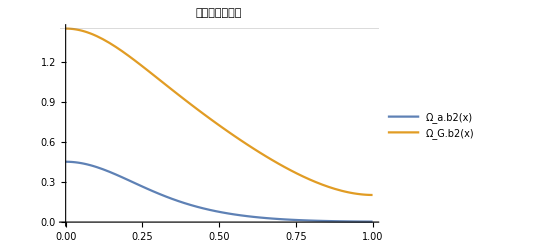

```mathematica
(*全局GAM本征值求解（增强稳定性与自动搜索版）*)(*模型方程：-ρ(x)^2/4 E0r''+D_rd(ω^2,x) E0r=0*)(*边界条件：E0r(0)=E0r(1)=0*)ClearAll["Global`*"];

(*===物理参数配置===*)
a=1.0;(*归一化小半径*)ρ0=0.01;(*归一化离子Larmor半径*)γi=5/3;(*离子绝热指数*)τ=1.0;(*温度比 T_e/T_i*)xmatch=0.3;(*初始匹配点*)(*===平衡剖面定义===*)q[x_]:=1.05+4*x^2;(*安全因子剖面*)T[x_]:=0.2+0.8*(1-x^2)^2;(*温度剖面*)(*===频率参数计算===*)Ωa2[x_]:=T[x]/(2*q[x]^2);(*声学连续区频率平方*)ΩG2[x_]:=T[x]*(1+1/(2*q[x]^2));(*GAM连续区频率平方*)(*===色散函数D_rd定义===*)NumeratorDrd[Ω2_,x_]:=(Ω2-Ωa2[x])*(Ω2-ΩG2[x]);
DenominatorDrd[Ω2_,x_]:=2*(γi+τ)*T[x]^2*Ω2+10^-6;
Drd[Ω2_,x_]:=NumeratorDrd[Ω2,x]/DenominatorDrd[Ω2,x];

(*===微分方程系统===*)
eqn[Ω2_]:={E0r''[x]==(4/(ρ0^2*T[x]))*Drd[Ω2,x]*E0r[x],E0r[0]==0,(*左边界条件*)E0r'[0]==0.0001  (*标准化初始导数*)};

(*===增强型射击法===*)
ShootingMethod[Ω2guess_]:=Module[{solLeft,solRight,logderivLeft,logderivRight,eps=10^-6},solLeft=Quiet@Check[NDSolve[eqn[Ω2guess],E0r,{x,0,xmatch},PrecisionGoal->10,AccuracyGoal->10,Method->{"StiffnessSwitching","NonstiffTest"->False}],$Failed];
solRight=Quiet@Check[NDSolve[{E0r''[x]==(4/(ρ0^2*T[x]))*Drd[Ω2guess,x]*E0r[x],E0r[1]==0,E0r'[1]==1},E0r,{x,xmatch,1},PrecisionGoal->10,AccuracyGoal->10,Method->{"StiffnessSwitching","NonstiffTest"->False}],$Failed];
If[solLeft===$Failed||solRight===$Failed,Return[10^6]];
logderivLeft=(E0r'[xmatch]/(E0r[xmatch]+eps))/.solLeft[[1]];
logderivRight=(E0r'[xmatch]/(E0r[xmatch]+eps))/.solRight[[1]];
(logderivLeft-logderivRight)/;NumericQ[logderivLeft]&&NumericQ[logderivRight]];

(*===自动计算连续谱范围===*)
Ωa2max=NMinValue[{Ωa2[x],0≤x≤1},x];
ΩG2min=NMaxValue[{ΩG2[x],0≤x≤1},x];


(*===检查连续谱间隙===*)
If[Ωa2max≥ΩG2min,Print["连续谱无间隙！Ωa.b2最大值 = ",Ωa2max," >= ΩG.b2最小值 = ",ΩG2min];
Abort[]];

(*===自适应参数搜索===*)
Ω2start=Ωa2max+0.01*(ΩG2min-Ωa2max);
Ω2end =ΩG2min-0.01*(ΩG2min-Ωa2max);
Ω2start
step=(Ω2end-Ω2start)/100;

Print["正在搜索本征值，范围：",Ω2start," 至 ",Ω2end];

Ω2solution=Catch[Do[currentGuess=Ω2start+k*step;
Print["尝试初始猜测：",currentGuess];
sol=Quiet@Check[Ω2/.FindRoot[ShootingMethod[Ω2],{Ω2,currentGuess,Ω2start,Ω2end},Method->"Secant",Evaluated->False,MaxIterations->50],$Failed];
If[NumericQ[sol]&&Ωa2max<sol<ΩG2min,Throw[sol];
Break[];],{k,0,100}]];

(*===结果验证与可视化===*)
If[NumericQ[Ω2solution],Print["成功找到本征值：Ω.b2 = ",Ω2solution];
FinalSolution=NDSolve[eqn[Ω2solution],E0r,{x,0,1},PrecisionGoal->10];
Plot[E0r[x]/.FinalSolution[[1]],{x,0,1},PlotLabel->Style[Row[{"Global GAM Mode (Ω.b2 = ",NumberForm[Ω2solution,{5,3}],")"}],14],AxesLabel->{"x","E0r"},ImageSize->500],Print["未找到有效解，请调整参数后重试"]];

(*===连续谱可视化===*)
Print["连续谱范围诊断："];
Plot[{Ωa2[x],ΩG2[x]},{x,0,1},PlotLegends->{"Ω_a.b2(x)","Ω_G.b2(x)"},PlotLabel->"连续谱频率范围",GridLines->{{},{Ωa2max,ΩG2min}}]
```

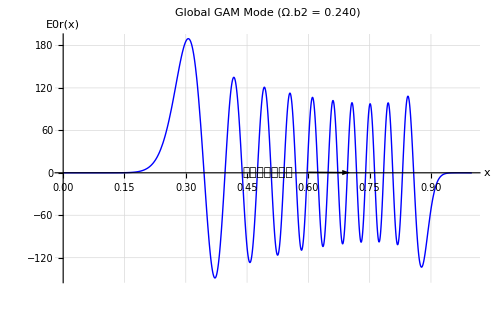

```mathematica
(*绘图参数优化*)Plot[E0r[x]/.FinalSolution[[1]],{x,0,1},PlotStyle->{Thick,Blue},PlotLabel->Style[Row[{"Global GAM Mode (Ω.b2 = ",NumberForm[Ω2solution,{5,3}],")"}],14,Bold],AxesLabel->{Style["x",14],Style["E0r(x)",14]},ImageSize->500,GridLines->Automatic,Prolog->{LightGray,Opacity[0.1],Rectangle[{0,-1},{1,1}]},Epilog->{Text[Style["连续谱间隙区域",12],{0.5,0.8},Background->White],Arrow[{{0.6,0.7},{0.7,0.3}}]}]
```